```mathematica
DetPoints=
{
{3000, 0.010333},
{1300, 0.016923},
{1200, 0.018182},
{1100,0.019403},
{1000,0.020870},
{900, 0.024444},
{800,0.021887},
{700,0.030000},
{600,0.028457},
{500,0.031098},
{400,0.035000},
{300,0.046161},
{200,0.076390},
{100,0.099872}
};
```

```mathematica
LPS=
{
{100,0.115900},
{200,0.091451},
{300,0.073274},
{400,0.067273},
{500,0.059395},
{600,0.057249},
{700,0.058576},
{800,0.056480},
{900,0.048424},
{1000,0.045980},
{1100,0.045239},
{1200,0.043892},
{1300,0.045023 },
{1400,0.046392},
{1500,0.045204},
{3000,0.027403}
};
```

```mathematica
Fib=
{
(*{1,1},
{2,0.853553},
{3,0.710042},
{5,0.516735},
{8,0.334845},
{13,0.235879},
{21,0.168727},
{34,0.12875},
{55,0.0923583},
{89,0.0619449},*)
{100,.062205},
{144,0.0436916},
{200,0.034656},
{233,0.033011},
{300,0.028740},
{377,0.024439},
{400,0.021869},
{500,0.019336},
{600,0.017426},
{610,0.017544},
{700,0.017065},
{800,0.014727},
{900,0.013625},
{987,0.01199},
{1000,0.011877},
{1100,0.011451},
{1200,0.011292},
{1300,0.010228},
{1400,0.009928},
{1500, 0.009174},
{1597,0.008791},
{2584,0.006149},
{3000,0.005789}(*,
{4181,0.004568},
{6765,0.003277},
{10946,0.002367}*)
};
```

```mathematica
sqrt3spiral=
{
{100, 0.061732},
{200,0.042712},
{300, 0.030685},
{400, 0.024324},
{500,0.020715},
{600, 0.017470},
{700, 0.015525},
{800, 0.015064},
{900, 0.013914},
{1000, 0.013516},
{1100,0.012222}, 
{1200,0.011957},
{1300,0.011158},
{1400,0.011342},
{1500,0.009936},
{3000,0.006612}
};

espiral=
{
{100, 0.064427},
{200, .037159},
{300, .029520},
{400, .025569},
{500, .023318},
{600,0.021306},
{700, 0.019770},
{800,0.017100},
{900,0.015229},
{1000,0.014380},
{1100,0.014248},
{1200,0.013635},
{1300, 0.012507},
{1400,0.011701},
{1500,0.011318},
{3000,0.006266}
};

smalliid={Table[i,{i,60}],ZZ}//Transpose;
```

Transpose::nmtx: The first two levels of {{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,«10»},ZZ} cannot be transposed.

```mathematica
ListPlot[Log[#]&@{ Fib,iid, DetPoints, LPS,  espiral, sqrt3spiral},PlotLegends->{"espiral", "fib", "3spiral", "lps", "det", "iid"}]
```

ListPlot::lpn: {{{0.,0.},{0.693147,-0.158348},{1.09861,-0.342431},{1.60944,-0.660225},{2.07944,-1.09409},{2.56495,-1.44444},«21»,{7.17012,-4.58263},{7.24423,-4.6124},{7.31322,-4.69138},{7.37588,-4.73403},{7.85709,-5.09147},{8.00637,-5.1518}},«4»,{«1»}} is not a list of numbers or pairs of numbers.

ListPlot[{{{0,0},{Log[2],-0.158348},{Log[3],-0.342431},{Log[5],-0.660225},{Log[8],-1.09409},{Log[13],-1.44444},{Log[21],-1.77947},{Log[34],-2.04988},{Log[55],-2.38208},{Log[89],-2.78151},{Log[100],-2.77732},{Log[144],-3.1306},{Log[200],-3.36228},{Log[233],-3.41091},{Log[300],-3.54947},{Log[377],-3.71158},{Log[400],-3.82269},{Log[500],-3.94579},{Log[600],-4.04979},{Log[610],-4.04304},{Log[700],-4.07073},{Log[800],-4.21807},{Log[900],-4.29585},{Log[987],-4.42368},{Log[1000],-4.43315},{Log[1100],-4.46968},{Log[1200],-4.48366},{Log[1300],-4.58263},{Log[1400],-4.6124},{Log[1500],-4.69138},{Log[1597],-4.73403},{Log[2584],-5.09147},{Log[3000],-5.1518}},Log[iid],{{Log[3000],-4.57241},{Log[1300],-4.07908},{Log[1200],-4.00732},{Log[1100],-3.94233},{Log[1000],-3.86944},{Log[900],-3.71137},{Log[800],-3.82186},{Log[700],-3.50656},{Log[600],-3.55936},{Log[500],-3.47061},{Log[400],-3.35241},{Log[300],-3.07562},{Log[200],-2.5719},{Log[100],-2.30387}},{{Log[100],-2.15503},{Log[200],-2.39195},{Log[300],-2.61355},{Log[400],-2.699},{Log[500],-2.82355},{Log[600],-2.86035},{Log[700],-2.83743},{Log[800],-2.87387},{Log[900],-3.02776},{Log[1000],-3.07955},{Log[1100],-3.0958},{Log[1200],-3.12602},{Log[1300],-3.10058},{Log[1400],-3.07063},{Log[1500],-3.09657},{Log[3000],-3.5971}},{{Log[100],-2.74222},{Log[200],-3.29255},{Log[300],-3.52269},{Log[400],-3.66637},{Log[500],-3.75853},{Log[600],-3.84877},{Log[700],-3.92359},{Log[800],-4.06868},{Log[900],-4.18455},{Log[1000],-4.24192},{Log[1100],-4.25114},{Log[1200],-4.29512},{Log[1300],-4.38147},{Log[1400],-4.44808},{Log[1500],-4.48136},{Log[3000],-5.07262}},{{Log[100],-2.78495},{Log[200],-3.15328},{Log[300],-3.48398},{Log[400],-3.71629},{Log[500],-3.8769},{Log[600],-4.04727},{Log[700],-4.1653},{Log[800],-4.19545},{Log[900],-4.27486},{Log[1000],-4.30388},{Log[1100],-4.40452},{Log[1200],-4.42644},{Log[1300],-4.4956},{Log[1400],-4.47924},{Log[1500],-4.61159},{Log[3000],-5.01887}}},PlotLegends→{espiral,fib,3spiral,lps,det,iid}]

Null

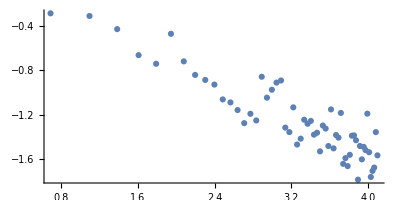

```mathematica
ZZ={1,0.7518147034224616,0.7341010729371646,0.6520206098031261,0.5157277119701125,0.4770997065829895,0.6251429673290732,0.48758974256352794,0.4316392078928158,0.41251687462879805,0.3955933048295717,0.34606629849791515,0.33683275639299176,0.31443850202264084,0.2794365228029032,0.30406994779265195,0.2863619883729834,0.42446311044634644,0.35153922265096127,0.37763180247396444,0.4027708749398481,0.41054925010880217,0.2684357803723918,0.2577581325464049,0.3221536928916279,0.2304652767340883,0.2429707307742811,0.28820869739826277,0.2779452241854955,0.2851159150327831,0.25193374005482516,0.2563201497891899,0.21669246453965696,0.273511910270194,0.26614725292181607,0.22734897282240968,0.3162384006538371,0.22264546070641628,0.2510782960232899,0.24525309376383153,0.30641370283878133,0.1936388544670804,0.20389757486892673,0.18973328355722063,0.21006025696908948,0.2495607090333345,0.25016550718916575,0.23950587595291278,0.16791092425667076,0.2274887869875426,0.2016624816230418,0.22562577546380425,0.21925715179639282,0.30439116207751754,0.2150026124445686,0.17205894305759,0.18177442177263398,0.1872814209782696,0.25775459579862087,0.20904922290654826};
ListPlot[Drop[Log[{Table[i,{i,60}],ZZ}]//Transpose,1],PlotRange->{0,-2},AspectRatio->1/2]
```

```mathematica
iid2= {
(*{10000, 0.016407},
{5000, 0.021554},*)
{3000,0.022515},
{1500,0.040082},
{1000,0.054649},
{800,0.068274},
{700,0.079368},
{600,0.085520},
{500,0.091648},
{400,0.093278},
{300,0.091655} ,
{200, 0.093360},
{100,0.194308}
};
```

```mathematica
iid =Union[ iid2,smalliid];
```

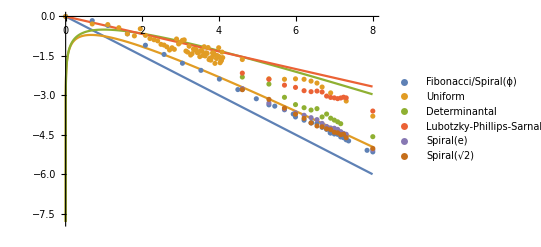

```mathematica
Show[Plot[{-3x/4,Log[(Sqrt[x]Exp[x]^(1/4)/Exp[x] )],Log[Sqrt[x](Exp[x]^(1/2)/Exp[x] )],Log[Exp[x]^(2/3)/Exp[x]]},{x,0,8}],
ListPlot[Log[#]&@{ Fib,iid, DetPoints, LPS, espiral, sqrt3spiral},PlotLegends->{"Fibonacci/Spiral(ϕ)", "Uniform", "Determinantal", "Lubotzky-Phillips-Sarnak", "Spiral(e)", "Spiral(√2)"}]]
```

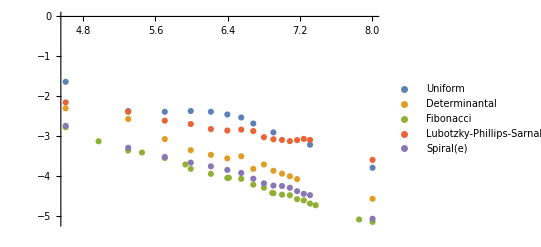

```mathematica
ListPlot[Log[#]&@{iid2, DetPoints, Fib, LPS,  espiral},PlotLegends->{"Uniform", "Determinantal", "Fibonacci","Lubotzky-Phillips-Sarnak", "Spiral(e)"}]
```

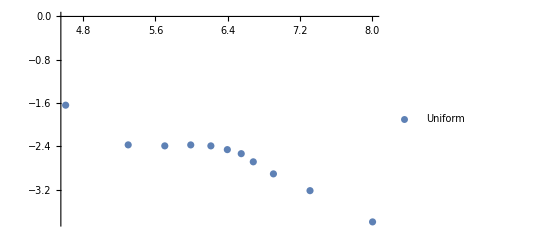

```mathematica
ListPlot[Log[#]&@{ iid2},PlotLegends->{"Uniform"}]
```

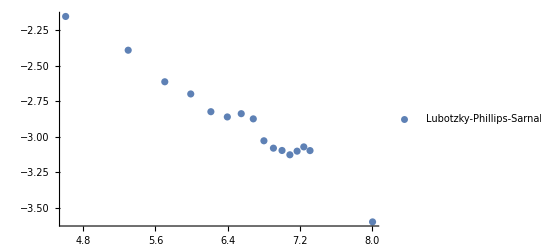

```mathematica
ListPlot[Log[#]&@{  LPS},PlotLegends->{ "Lubotzky-Phillips-Sarnak"}]
```

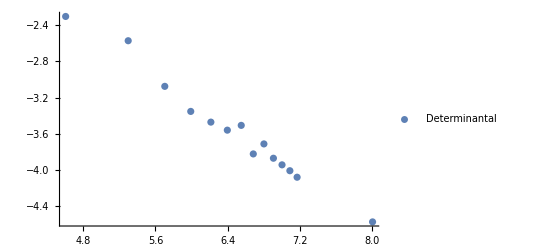

```mathematica
ListPlot[Log[#]&@{ DetPoints},PlotLegends->{"Determinantal"}]
```

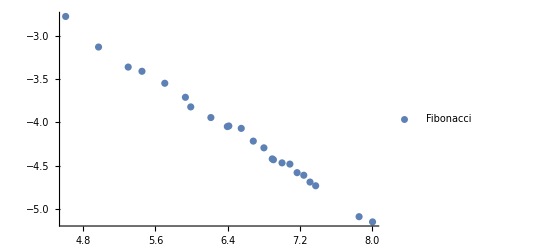

```mathematica
ListPlot[Log[#]&@{ Fib},PlotLegends->{"Fibonacci"}]
```

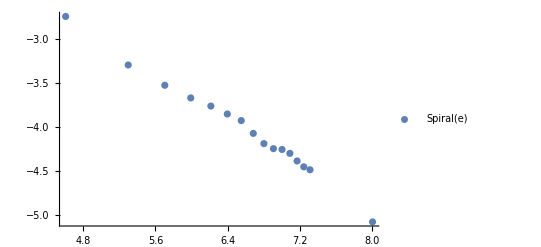

```mathematica
ListPlot[Log[#]&@{ espiral},PlotLegends->{ "Spiral(e)"}]
```